Sin[(π U)/250]^2

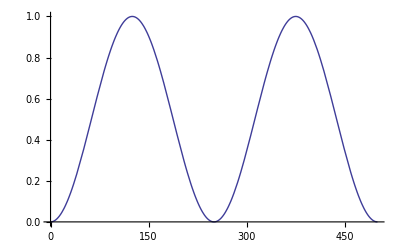

```mathematica
Ι=Sin[2π U/500]^2
Plot[Ι,{U,0,500}]
```

{U→U0+A Sin[10 t]}

{U0→125,A→30}

{U0→200,A→30}

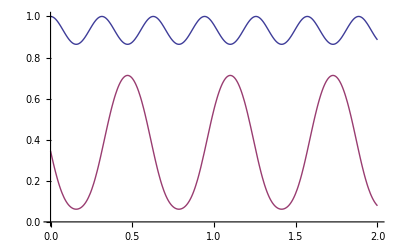

```mathematica
l1={U->U0+A Sin[10t]}
l2a={U0->125,A->30}
l2b={U0->200,A->30}
Plot[{Ι/.l1/.l2a,Ι/.l1/.l2b},{t,0,2},PlotRange->{0,1}]
```

```mathematica
Plot3D[Sin[2π(U0+A Sin[2 π t])/500]^2/.A->20,{U0,0,330},{t,0,3},ImageSize->500]
```

-Graphics3D-